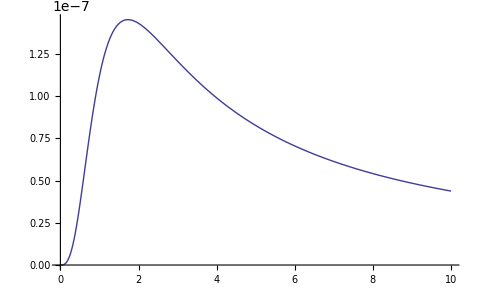

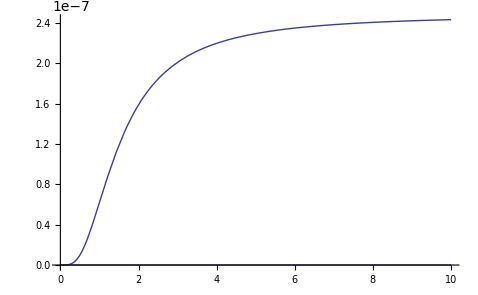

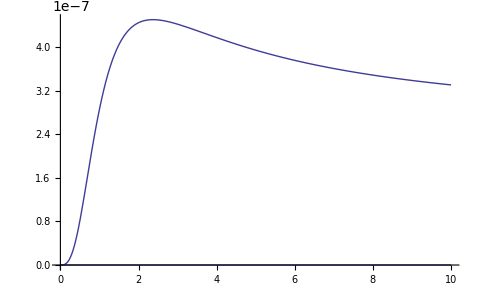

Plot::nonopt: Options expected (instead of {r, 0, 200}) beyond position 2 in Plot[{dϕ + 2\ V, 0}, {a2, 0, 10}, {r, 0, 200}, PlotRange → All]. An option must be a rule or a list of rules.

Plot[{dϕ+2 V,0},{a2,0,10},{r,0,200},PlotRange→All]

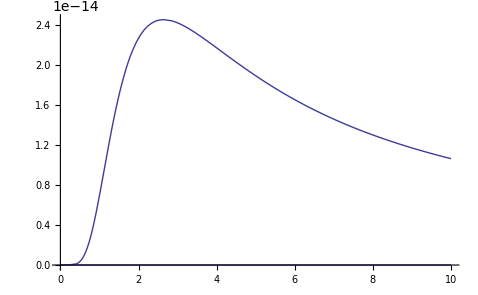

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{{1,2.37063},{2,2.3706},{3,2.37057},{4,2.37054},{5,2.37051},{6,2.37048},{7,2.37045},{8,2.37043},{9,2.3704},{10,2.37037},{11,2.37034},{12,2.37031},{13,2.37028},{14,2.37025},{15,2.37022},{16,2.37019},{17,2.37016},{18,2.37014},{19,2.37011},{20,2.37008},{21,2.37005},{22,2.37002},{23,2.36999},{24,2.36996},{25,2.36993},{26,2.3699},{27,2.36988},{28,2.36985},{29,2.36982},{30,2.36979},{31,2.36976},{32,2.36973},{33,2.3697},{34,2.36967},{35,2.36964},{36,2.36961},{37,2.36959},{38,2.36956},{39,2.36953},{40,2.3695},{41,2.36947},{42,2.36944},{43,2.36941},{44,2.36938},{45,2.36935},{46,2.36933},{47,2.3693},{48,2.36927},{49,2.36924},{50,2.36921},{51,2.36918},{52,2.36915},{53,2.36912},{54,2.36909},{55,2.36907},{56,2.36904},{57,2.36901},{58,2.36898},{59,2.36895},{60,2.36892},{61,2.36889},{62,2.36886},{63,2.36883},{64,2.36881},{65,2.36878},{66,2.36875},{67,2.36872},{68,2.36869},{69,2.36866},{70,2.36863},{71,2.3686},{72,2.36857},{73,2.36855},{74,2.36852},{75,2.36849},{76,2.36846},{77,2.36843},{78,2.3684},{79,2.36837},{80,2.36834},{81,2.36831},{82,2.36829},{83,2.36826},{84,2.36823},{85,2.3682},{86,2.36817},{87,2.36814},{88,2.36811},{89,2.36808},{90,2.36806},{91,2.36803},{92,2.368},{93,2.36797},{94,2.36794},{95,2.36791},{96,2.36788},{97,2.36785},{98,2.36782},{99,2.3678},{100,2.36777},{101,2.36774}}

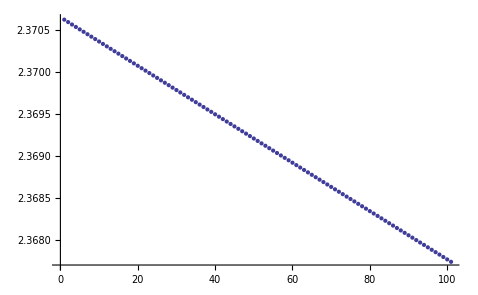

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{4.50377×10^-7,{a2→2.37063}}

{2.45424×10^-8,{a2→2.64353}}

```mathematica
σ=8.0;
r0=120;
ϕ0=(a2^2 E^(-a2^2)+0.5(1-Tanh[2(1-Abs[a2])]))/40;
ϕ0=(a2^2/(1+a2^2))0.001642;
ϕ=ϕ0 E^((-(r-r0)^2)/σ);
dϕ=(D[ϕ, r])^2;
dϕ0=%/.r->r0+√(σ/2);
V=1/(32 π a2)(1-E^(4 √(π/3)ϕ))^2 E^(-8 √(π/3)ϕ);
Plot[V/.r->r0,{a2,0,10},PlotRange->All]
Plot[{dϕ,0}/.r->r0+√(σ/2),{a2,0,10},PlotRange->All]
Plot[{dϕ0+2V,0}/.r->r0,{a2,0,10},PlotRange->All]

Plot[{dϕ+2V,0},{a2,0,10},{r,0,200},PlotRange->All]

Plot[{dϕ0 V,0}/.r->r0,{a2,0,10},PlotRange->All]
data=Table[FindMaximum[(dϕ0+2V ψ^4)/.r->r0,{a2,2}],{ψ,1,1.001,0.00001}];
n=Length[data];
Table[{i,a2}/.data[[i,2]],{i,n}]
ListPlot[%]
FindMaximum[(dϕ0 +2V)/.r->r0,{a2,2}]
FindMaximum[10^6(dϕ0 V)/.r->r0,{a2,2}]
```

```mathematica
data[[1,2]]
```

{a2→3.28047}

```mathematica
N[10^(3.4/8)]
```

2.66073

```mathematica
X
```